```mathematica
$RecursionLimit = 100000;
Go[x_,y_]:= Switch[a[[y,x]],0,a[[y,x]]=1,1,a[[y,x]]=2; 1+Go[x,y+1],2,a[[y,x]]=3; 1+Go[x-1,y],3,a[[y,x]]=4; 1+ Go[x+1,y], 4,a[[y,x]]=1; 1+Go[x,y-1]]
```

```mathematica
a = Table[0,{100},{100}];0;
```

```mathematica
t=Table[Go[50,50],{Ceiling[10^2π]}];//Timing
```

{0.125,Null}

```mathematica
t=Table[Go[50,50],{Ceiling[20^2π]}];//Timing
```

```mathematica
t=Table[Go[50,50],{Ceiling[25^2π]}];//Timing
```

{4.35938,Null}

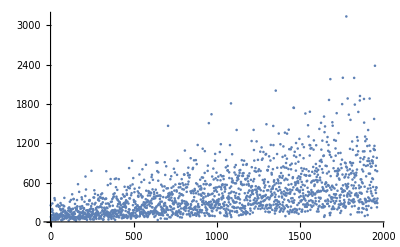

```mathematica
ListPlot[t,PlotRange->All]
```

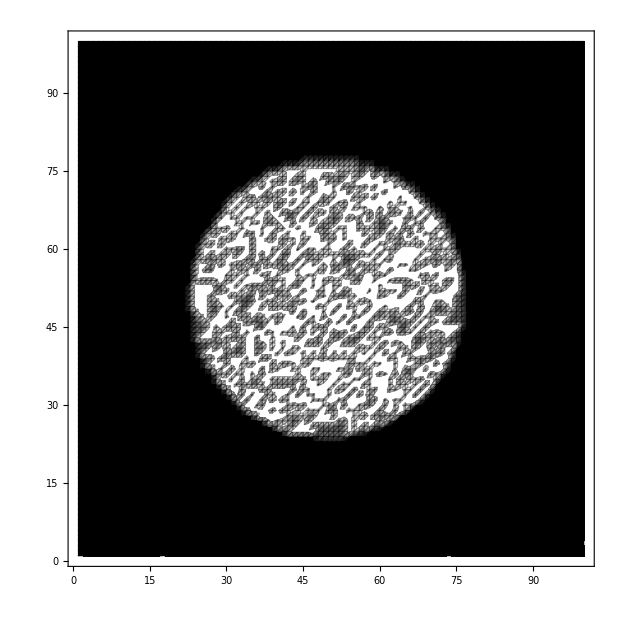

```mathematica
ListDensityPlot[a,ColorFunction->GrayLevel,Mesh->All]
```